## Visualizing distances between the users

Loading the data

```mathematica
csvReviews=Take[Drop[Import["/tmp/reviews_all.csv","CSV"],1],100000]
```

{{5,213719,16007298},{5,198763,16007298},{5,239184,16007298},{5,238654,16007298},{5,230116,16007298},{5,245403,16007298},{5,12141,16007298},{5,23032,16007298},{5,269891,16007298},{5,194425,16007298},{5,223085,16007298},{5,278099,16007298},{5,238162,16007298},{5,86331,16007298},{5,230281,16007298},{5,218790,16007298},{5,15821,16007298},{5,256018,16007298},{5,67789,16007298},{5,15931,16007298},{5,255335,16007298},{5,215014,16007298},99957,{5,121411,1471732},{5,216190,1471732},{5,26692,1471732},{5,74437,1471732},{5,16504,1471732},{5,13206,1471732},{5,25203,1471732},{5,44839,1471732},{5,13651,1471732},{5,24332,1471732},{2,127501,1471732},{3,12471,359494},{5,143069,9990898},{5,24069,9990898},{5,229508,9990898},{5,236942,2447592},{5,17066,11403286},{5,24473,11403286},{5,26257,11403286},{4,203769,7510857},{5,25451,14048996}}
 |  |  |  |

Getting a list of all the authors

```mathematica
authors=DeleteDuplicates[#[[3]]&/@csvReviews]
```

Associating every author with its reviews

```mathematica
users=Table[author->DeleteCases[Table[If[review[[3]]==author,Drop[review,{3}]],{review,csvReviews}],Null],{author,authors}]
```

{16007298→{{5,213719},{5,198763},{5,239184},{5,238654},{5,230116},{5,245403},{5,12141},{5,23032},{5,269891},{5,194425},{5,223085},{5,278099},{5,238162},{5,86331},{5,230281},{5,218790},{5,15821},{5,256018},{5,67789},{5,15931},{5,255335},{5,215014},{5,213505},{5,233923},{5,76278},{5,15413},{5,235589},{5,13325},{5,55451},{5,218180},{5,142481},{5,25331},{5,19307},{5,255362},{5,255361},{5,11693},{5,209990},{5,9115},532,{5,56927},{5,14316},{5,143082},{5,214488},{5,77156},{5,8493},{5,9044},{5,51301},{5,16120},{5,152239},{5,10638},{5,229272},{5,98390},{5,11406},{5,14556},{5,23534},{5,20144},{5,25971},{5,229923},{5,146100},{5,221000},{5,9249},{5,56999},{5,139580},{5,16592},{5,221988},{5,20021},{5,15057},{5,24132},{5,10813},{5,17165},{5,10222},{5,19247},{5,9471},{5,10687},{5,10402},{5,31965},{5,241430}},4938,14048996→1}
 |  |  |  |

Fitting a dimension reducer

```mathematica
dimensionReducer=DimensionReduction[Flatten[Join[Values[#]//First,Table[review,{review,Values[#]}]]]&/@users,Method->"Linear"]
```

DimensionReducerFunction[…]

Applying the dimensionality reduction to our data

```mathematica
users2D=(Keys[#]->dimensionReducer[Flatten[Join[Values[#]//First,Table[review,{review,Values[#]}]]]])&/@users
```

{16007298→{0.155663,-0.16671},2012871→{-0.0731174,-0.337524},9020456→{0.413375,0.0487773},1922840→{0.411156,0.0484272},286648→{-0.966066,-0.740453},3672150→{0.390562,0.0512373},731327→{0.401412,0.0482864},430608→{0.408628,0.0482791},594098→{0.40627,0.0501646},775411→{-4.95718,-0.28721},4920,15471065→{0.391145,0.0517223},15777604→{0.400428,0.0453685},5901381→{0.415527,0.0492111},1471732→{0.403905,0.0479741},359494→{0.415405,0.0492234},9990898→{0.399426,0.0495313},2447592→{0.388339,0.0520115},11403286→{0.414395,0.0493765},7510857→{0.392339,0.0515993},14048996→{0.41384,0.0493848}}
 |  |  |  |

Applying the dimensionality reduction to our data

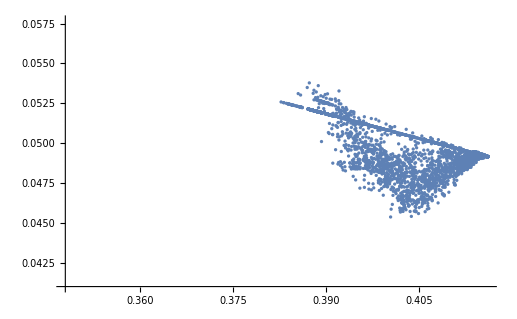

```mathematica
ListPlot[Values[#]&/@users2D]
```

## Visualizing data about the users

Loading the data

```mathematica
csvProfiles=Drop[Import["/tmp/profiles_all.csv","CSV"],1]
```

{{3771717,cheri,,[none selected],,},{9020456,Mariwanna,,united states,Maryland,Baltimore},{13145275,Tyler Bradley,,[none selected],,},{6613609,Terrie Melcher Murphy,,,,},{16194924,cheri,,[none selected],,},{21140057,cheri,,[none selected],,},{7222641,toto858,,[none selected],,},{8919808,70sdonna,,[none selected],,},{6294607,Margo Pfeifer,,,,},{15700044,Barb Fredricks,,,,},2412931,{17473495,Ashlee Jones,,,,},{16560257,Gaby Sunderland,,,,},{17340542,Austin Leifi,,,,},{16043773,Nate James,,,,},{20477386,Rhianon Solomon,,,,},{7460924,Lora Marie,,,,},{21829435,Laura Kicker,,,,},{17904570,Kelly Dalessio,,,,},{14773527,Rhonda Roberts,,,,}}
 |  |  |  |

Creating a list of all the countries

```mathematica
countries=Capitalize[DeleteCases[If[#[[4]]=="[none selected]"||#[[4]]=="","other/not selected",#[[4]]]&/@csvProfiles,None],"TitleCase"]
```

{Other/Not Selected,United States,Other/Not Selected,Other/Not Selected,Other/Not Selected,Other/Not Selected,Other/Not Selected,Other/Not Selected,Other/Not Selected,Other/Not Selected,United States,United States,Other/Not Selected,Other/Not Selected,Other/Not Selected,Other/Not Selected,Other/Not Selected,Other/Not Selected,United States,Other/Not Selected,2412910,Other/Not Selected,Other/Not Selected,Other/Not Selected,Other/Not Selected,Other/Not Selected,Other/Not Selected,Other/Not Selected,Other/Not Selected,Other/Not Selected,Other/Not Selected,Other/Not Selected,Other/Not Selected,Other/Not Selected,Other/Not Selected,Other/Not Selected,Other/Not Selected,Other/Not Selected,Other/Not Selected,Other/Not Selected,Other/Not Selected}
 |  |  |  |

Extracting countries data

```mathematica
countriesFrequence=(#->Count[countries,#])&/@DeleteDuplicates[countries]
```

Plotting the regions

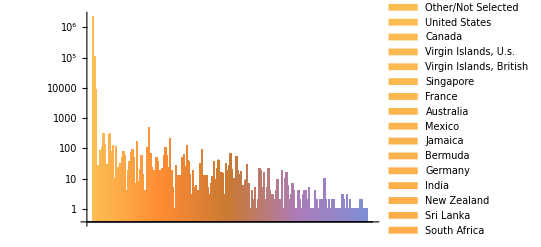

```mathematica
BarChart[{Values[countriesFrequence]},ChartLegends->Keys[countriesFrequence],ScalingFunctions->"Log"]
```

Calculate the percentages

```mathematica
percentages=DeleteCases[(Interpreter["Country"][#]->N[(Association[countriesFrequence][#]*100)/Total[Values[countriesFrequence]]])&/@DeleteCases[Keys[countriesFrequence],"Other/Not Selected"]Null]
```

Plot on a world map

```mathematica
GeoBubbleChart[percentages]
```

-Graphics-

Visualizing the tastes of U.S. users

```mathematica
usTastes=DeleteCases[If[#[[4]]!="united states"||Not[MemberQ[Keys[users2D],#[[1]]]],None,users2D[#[[1]]]]&/@csvProfiles,None]
```

Making a plot

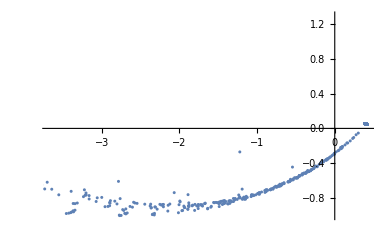

```mathematica
ListPlot[usTastes]
```

## Visualizing distances between the recipes

Loading the data

```mathematica
csvRecipes=Drop[Import["/tmp/recipes.csv","CSV"],1]
```

{{6663,[{"id":16238,"text":"1/2 cup Parmesan cheese","quantity":40.0},{"id":16406,"text":"3/4 teaspoon ground black pepper","quantity":1.57499993},{"id":16396,"text":"1/2 teaspoon garlic powder","quantity":1.38833332},{"id":2329,"text":"1 (17.5 ounce) package frozen puff pastry, thawed","quantity":490.0},{"id":16318,"text":"1 egg white","quantity":33.4}]},95129,{207304,[{"id":0,"text":"Batter:","quantity":0.0},{"id":1336,"text":"4 (1 ounce) squares unswe…","quantity":29.75},{"id":1527,"text":"2 cups sifted powdered sugar","quantity":250.8}]}}
 |  |  |  |

Getting all the recipes ingredients

```mathematica
recipes=((#//First)->Table[Association[currentIngredient][["id"]],{currentIngredient,ImportString[StringJoin[Select[Characters[#[[2]]],PrintableASCIIQ]],"JSON"]}])&/@csvRecipes
```

{6663→{16238,16406,16396,2329,16318},6664→{16339,4397,1631,1684,1526,2356,16421,2359,16287,16317,443,4317,12338,16159},6665→{2496,6311,1526,16421,2496,2362,1684,16317},6666→{1526,6379,16317,1684,2359,16421,16386,16401,2496,4557,3810},6667→{2362,16278,1526,1767,16421,16157},6668→{16157,1526,16278,2362,1686,1526,16317,5140,5145,16421},95120,195176→{4175,18864},195263→{3103,4397,26852,1718},123362→{1631,1684,1526,2356,16421,16317,16278,6300},206912→{21429,1536,21316},207304→{0,1336,16157,16406,16317,1526,16424,8314,1684,16421,2356,3819,0,0,1336,1338,16157,8314,16258,1527}}
 |  |  |  |

Applying the dimensionality reduction to our data

```mathematica
recipes2D=AssociationThread[Keys[recipes],DimensionReduce[Values[recipes],Method->"Linear"]]
```

<|6663→{-0.932952,-0.707267},6664→{0.985418,0.68257},6665→{1.90016,0.755415},6666→{0.581578,0.372414},6667→{-0.0830507,0.859058},6668→{0.998631,0.700727},6669→{1.29309,0.790004},6670→{1.47406,0.695382},6671→{2.362,0.610974},6672→{0.673806,0.413596},6673→{-0.226909,0.0106009},95110,247222→{3.13947,0.052905},247224→{0.658275,-0.0845572},194440→{0.0967534,0.0974819},195173→{1.01517,0.330533},195175→{0.958892,0.64575},195176→{-0.47511,-0.429728},195263→{-3.35229,3.41717},123362→{0.336475,0.802206},206912→{-3.63879,3.5842},207304→{0.759299,0.807547}|>
 |  |  |  |

Plot all the recipes

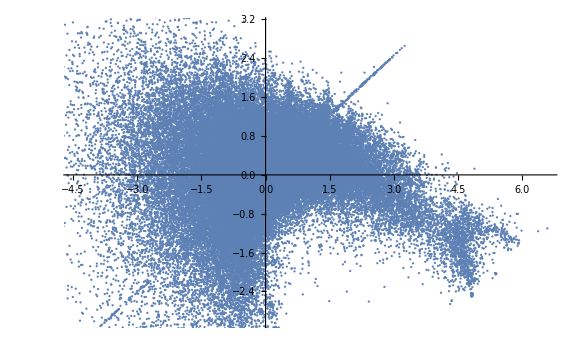

```mathematica
ListPlot[Values[recipes2D]]
```

## Using Deep Learning to predict wether an users might or might not like a food

Creating associations for users and recipes

```mathematica
users2DAssociation=Association[users2D]
```

<|16007298→{0.155663,-0.16671},2012871→{-0.0731174,-0.337524},9020456→{0.413375,0.0487773},1922840→{0.411156,0.0484272},286648→{-0.966066,-0.740453},3672150→{0.390562,0.0512373},731327→{0.401412,0.0482864},430608→{0.408628,0.0482791},594098→{0.40627,0.0501646},775411→{-4.95718,-0.28721},4920,15471065→{0.391145,0.0517223},15777604→{0.400428,0.0453685},5901381→{0.415527,0.0492111},1471732→{0.403905,0.0479741},359494→{0.415405,0.0492234},9990898→{0.399426,0.0495313},2447592→{0.388339,0.0520115},11403286→{0.414395,0.0493765},7510857→{0.392339,0.0515993},14048996→{0.41384,0.0493848}|>
 |  |  |  |

```mathematica
recipes2DAssociation=Association[recipes2D]
```

<|6663→{-0.932952,-0.707267},6664→{0.985418,0.68257},6665→{1.90016,0.755415},6666→{0.581578,0.372414},6667→{-0.0830507,0.859058},6668→{0.998631,0.700727},6669→{1.29309,0.790004},6670→{1.47406,0.695382},6671→{2.362,0.610974},6672→{0.673806,0.413596},6673→{-0.226909,0.0106009},95110,247222→{3.13947,0.052905},247224→{0.658275,-0.0845572},194440→{0.0967534,0.0974819},195173→{1.01517,0.330533},195175→{0.958892,0.64575},195176→{-0.47511,-0.429728},195263→{-3.35229,3.41717},123362→{0.336475,0.802206},206912→{-3.63879,3.5842},207304→{0.759299,0.807547}|>
 |  |  |  |

Preparing the reviews (getting data from the CSV file and associating them with a rating)

```mathematica
usersReviews=Association[Table[author->DeleteCases[Table[If[review[[3]]==author,review[[2]]],{review,csvReviews}],Null],{author,authors}]]
```

<|16007298→{213719,198763,239184,238654,230116,245403,12141,23032,269891,194425,223085,278099,238162,86331,230281,218790,15821,256018,67789,15931,255335,215014,213505,233923,76278,15413,235589,13325,55451,218180,142481,25331,19307,255362,255361,11693,209990,9115,94570,230049,230122,15213,255359,255360,255356,240245,23813,9253,51283,47724,231351,240751,230749,235278,232363,235272,15994,12538,255357,12293,244458,73423,217975,255358,223297,18830,8495,239047,244876,254690,254686,254685,254687,254689,241614,245267,246655,244867,254694,245221,234664,73634,228859,215309,186965,236776,254692,254691,254693,254698,254695,254699,254696,254697,21134,77797,229423,239808,234909,235814,228319,88086,219963,89334,400,232096,171407,223284,24094,15836,12322,12235,218791,87438,145194,214644,222850,39748,223302,91353,20725,14581,14565,17048,214709,222512,149591,12340,21694,170876,8546,215622,20019,18443,13436,146819,216459,92359,217944,153660,6897,89403,244597,218311,131107,13079,51147,240064,132814,19490,25642,9247,100663,220468,10549,24609,75133,15070,23176,15436,192666,189930,79805,77194,222243,23600,235270,20156,8652,212381,15206,56927,14316,143082,214488,77156,8493,9044,51301,16120,152239,10638,229272,98390,11406,14556,23534,20144,25971,229923,146100,221000,9249,56999,139580,16592,221988,20021,15057,24132,10813,17165,10222,19247,9471,10687,10402,31965,241430},4938,1|>
 |  |  |  |

```mathematica
reviews=Association[((#[[2]])->(#//First))&/@csvReviews]
```

<|213719→5,198763→5,239184→5,238654→3,230116→5,245403→5,12141→1,23032→5,269891→5,194425→2,223085→5,278099→5,238162→5,86331→5,230281→5,218790→5,15821→5,256018→5,67789→3,15931→4,255335→5,215014→5,213505→5,233923→5,76278→4,15413→5,235589→5,13325→5,55451→5,218180→5,142481→5,25331→4,19307→5,255362→5,255361→5,11693→5,209990→5,9115→5,94570→2,230049→5,230122→5,15213→4,255359→5,255360→5,255356→5,240245→5,23813→3,9253→5,51283→1,47724→5,231351→5,240751→5,230749→4,235278→5,232363→4,235272→5,15994→4,12538→5,42191,104869→5,64077067→4,64077075→4,100839→3,63848876→5,223518→5,151538→4,63113441→5,62793218→5,55249928→5,83652→4,123229→2,14594→4,63686→4,216309→5,62207634→5,121299→4,270594→5,64346178→5,228015→5,62147001→5,62144851→5,62143736→5,77013→4,241372→5,234186→5,72845→4,64251→4,23245→5,10020→5,237427→4,162202→5,122621→5,121137→5,187155→5,64468055→5,82203→4,33290→4,13266→5,11650→4,46960→5,237888→5,219569→4,217094→5,232790→5,215739→5,64149547→5,62364662→5,62364648→5,234654→5,229094→4,17648→3,200340→5,267700→5,121411→5,127501→2,12471→3,203769→4|>
 |  |  |  |

Creating the dataset

```mathematica
dataset=Table[Table[Join[users2DAssociation[user],recipes2DAssociation[recipe]]->If[reviews[recipe]>=4,True,False],{recipe,usersReviews[user]}],{user,Keys[usersReviews]}]//First
```

Cleaning up the dataset

```mathematica
cleanedDataset=DeleteCases[(If[ListQ[Keys[#]],#,Null])&/@dataset,Null]
```

Creating the Deep Neural Network

```mathematica
chain=NetChain[{
LinearLayer[4],Ramp,

LinearLayer[128], Ramp, DropoutLayer[0.2],
LinearLayer[128], Ramp, DropoutLayer[0.2],
LinearLayer[128], Ramp, DropoutLayer[0.2],
LinearLayer[128], Ramp, DropoutLayer[0.2],
LinearLayer[128], Ramp, DropoutLayer[0.2],
LinearLayer[128], Ramp, DropoutLayer[0.2],

LinearLayer[2],SoftmaxLayer[]
},"Input"->4,"Output"->NetDecoder[{"Class",{True,False}}]]
```

NetChain[<>]

Training the Deep Neural Network

```mathematica
model=NetTrain[chain,cleanedDataset,ValidationSet->Scaled[0.2],BatchSize->128]
```

NetChain[<>]

Measuring Neural Network’s accuracy

```mathematica
ClassifierMeasurements[model,cleanedDataset,"Accuracy"]
```

0.932343

## Finding similar recipes

Fitting a dimensionality reduction function on the recipes and on the users

```mathematica
recipesDimensionalityReduction=DimensionReduction[Values[recipes],Method->"Linear"]
```

DimensionReducerFunction[…]

Getting 3 sample recipes

```mathematica
sampleRecipes=RandomSample[recipes,3]
```

{14510→{16157,16420,7428,18845,16428,4311},146478→{16157,4397,4432,4292,5489,16278,16215,16407,7428,16404,25387,21267,16238},183288→{1525,16386,16223,16312,16424,4978,3819,11188,3819}}

Compute the 2D position of each recipe and plotting them

```mathematica
sampleRecipes2D=AssociationThread[recipiesDimensionalityReduction[Values[sampleRecipes]],Keys[sampleRecipes]]
```

<|{-0.528366,-1.81385}→14510,{-1.0624,-0.546329}→146478,{0.0432639,-0.652252}→183288|>

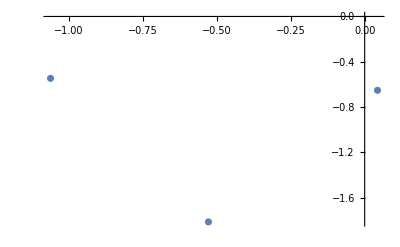

```mathematica
ListPlot[Keys[sampleRecipes2D]]
```

Creating a recipe index

```mathematica
recipesIndex=AssociationThread[Values[recipes2D],Keys[recipes2D]]
```

<|{-0.932952,-0.707267}→6663,{0.985418,0.68257}→6664,{1.90016,0.755415}→6665,{0.581578,0.372414}→6666,{-0.0830507,0.859058}→6667,{0.998631,0.700727}→6668,{1.29309,0.790004}→6669,{1.47406,0.695382}→6670,{2.362,0.610974}→6671,{0.673806,0.413596}→6672,{-0.226909,0.0106009}→6673,{-0.280432,0.430453}→6674,{0.350019,0.585328}→6675,{1.5431,0.810775}→6676,94100,{1.84672,0.392131}→121646,{-2.5214,-1.1018}→246789,{0.272744,0.914196}→246918,{-0.536669,-1.09069}→247059,{5.92626,-1.34733}→247221,{3.13947,0.052905}→247222,{0.658275,-0.0845572}→247224,{1.01517,0.330533}→195173,{0.958892,0.64575}→195175,{-0.47511,-0.429728}→195176,{-3.35229,3.41717}→195263,{0.336475,0.802206}→123362,{-3.63879,3.5842}→206912,{0.759299,0.807547}→207304|>
 |  |  |  |

Removing samples from index if they exists

```mathematica
Do[KeyDropFrom[recipesIndex,recipe],{recipe,sampleRecipes2D}]
```

Calculating the mean of the sample recipes and plotting it

```mathematica
meanRecipe=N[Mean[Keys[sampleRecipes2D]]]
```

{-0.515834,-1.00415}

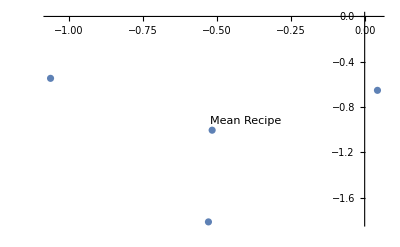

```mathematica
ListPlot[Join[Keys[sampleRecipes2D],{Labeled[meanRecipe,"Mean Recipe"]}]]
```

Getting the nearest recipes and plotting them

```mathematica
nearestRecipes=Nearest[Keys[recipesIndex],meanRecipe,10]
```

{{-0.526253,-1.00251},{-0.527397,-1.00116},{-0.505426,-0.996582},{-0.520642,-1.01813},{-0.505088,-1.02006},{-0.535978,-1.00413},{-0.522819,-1.02307},{-0.51917,-1.02638},{-0.530649,-1.02107},{-0.516495,-1.02765}}

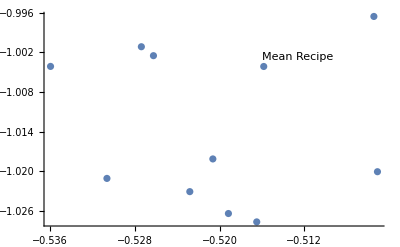

```mathematica
ListPlot[Join[nearestRecipes,{Labeled[meanRecipe,"Mean Recipe"]}]]
```

Getting the IDs

```mathematica
nearestRecipesIDs=recipesIndex[#]&/@nearestRecipes
```

{274672,149702,121608,80929,256154,213774,229942,278305,38402,245651}